```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/github_public_repos/d-Cubic/examples/test_deriv_p_boundary_1d

Grid

```mathematica
grid=Import["test_deriv_p_boundary_1d.txt","Table"];
```

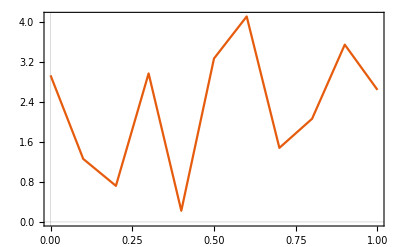

```mathematica
ListLinePlot[grid]
```

```mathematica
xSpacing=Abs[grid[[2,1]]-grid[[1,1]]]
```

0.1

Analytic formula

```mathematica
derivp1=1-1. x-0.5 x^2+0.5 x^3
```

1-1. x-0.5 x^2+0.5 x^3

```mathematica
derivp2=1. x+1. x^2-1. x^3
```

1. x+1. x^2-1. x^3

```mathematica
derivp3=-0.5 x^2+0.5 x^3
```

-0.5 x^2+0.5 x^3

Test point

```mathematica
xTest=0.023;
```

Convert to fraction

```mathematica
pt1=Select[grid,#[[1]]>xTest-xSpacing&&#[[1]]<xTest&][[1]]
```

{0,2.93873}

```mathematica
xFrac=(xTest-pt1[[1]])/xSpacing
```

0.23

Evaluate test

```mathematica
derivp1/.x->xFrac
```

0.749634

```mathematica
derivp2/.x->xFrac
```

0.270733

```mathematica
derivp3/.x->xFrac
```

-0.0203665